# Holographic Entanglement Entropy

Rob Myers problem for the Mathematica School

# Zero Temperature

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[r, 0]]
Symbolize[Subscript[θ, 0]]
Symbolize[Subscript[θ, max]]
```

```mathematica
ℒ=√(r[θ]^2+(D[r[θ], θ])^2/f[r[θ]])/.f->(r↦r^2/L^2+1);
```

```mathematica
Subscript[r, 0]=L Cos[Subscript[θ, 0]]/(√(Sin[Subscript[θ, 0]]^2-Sin[#]^2))&;
```

```mathematica
D[(D[ℒ, D[r[θ], θ]]), θ]-D[ℒ, r[θ]];
Solve[%==0,r''[θ]]//FullSimplify//First;
eom=r''[θ]-(r''[θ]/.%)==0
```

-r[θ]-r[θ]^3/L^2-((2 L^2+3 r[θ]^2) r'[θ]^2)/(r[θ] (L^2+r[θ]^2))+r''[θ]==0

```mathematica
eom/.r->Subscript[r, 0]//FullSimplify
```

True

```mathematica
Subscript[θ, max]=θ/.Solve[Subscript[r, 0][θ]==L^2/δ,θ]⟦2⟧//Series[#,{δ,0,2}]&//FullSimplify//PowerExpand//Quiet
```

θ_0-(Cot[θ_0] δ^2)/(2 L^2)+O[δ]^3

```mathematica
toIntegrate=ℒ/.r->Subscript[r, 0]//FullSimplify//PowerExpand
```

(L Sin[2 θ_0])/(Cos[2 θ]-Cos[2 θ_0])

```mathematica
integrated=Integrate[toIntegrate,θ]
```

L (-1/2 Csc[2 θ_0] Log[Sin[θ-θ_0]]+1/2 Csc[2 θ_0] Log[Sin[θ+θ_0]]) Sin[2 θ_0]

```mathematica
result=Series[(integrated/.θ->Subscript[θ, max])-(integrated/.θ->0),{δ,0,0}]//FullSimplify[#,{0<Subscript[θ, 0]<π/2,L>0,δ>0}]&//Normal//Quiet
```

L Log[(2 L Sin[θ_0])/δ]

```mathematica
prefactor=(2 π^((d-1)/2)/Gamma[(d-1)/2])/(4G)/.d->2;
```

```mathematica
result*prefactor
```

(L Log[(2 L Sin[θ_0])/δ])/(2 G)

In agreement with (8)

# Finite Temperature

## RT Geodesic in AdS_3 black hole

```mathematica
Clear[ro,rh,eulereq,eq,Θo,Geor,GeodesicC,Geodesic,h]
```

Ads Radius “L” and IR cutoff “Rmax”

```mathematica
Clear[L,Rmax]
L=1;
Rmax=1000;
```

“Lagrangian” for the RT surface

```mathematica
Clear[Lagran]
Lagran = Sin[θ]^(d-2)r[θ]^(d-2)√(r[θ]^2+(D[r[θ], θ])^2/f[r[θ]]);
```

Euler-Lagrange equations

```mathematica
Needs["VariationalMethods`"]
eulereq=EulerEquations[Lagran,r[θ],θ]⟦1⟧;
```

```mathematica
Clear[f,μ]
f[r_]:=r^2/L+1-μ/r^(d-2) ;μ=rh^(d-2)(rh^2/L^2+1);
```

extremizing the area or length of geodesic

```mathematica
eq[rh_]=(r''[θ]-(eulereq/.d->2/.{r''[θ]->y}//Solve[#==0,y]&//FullSimplify)⟦1,1,2⟧)
```

-((-rh^2 r[θ]+r[θ]^3)^2+(-2 rh^2+3 r[θ]^2) r'[θ]^2)/(-rh^2 r[θ]+r[θ]^3)+r''[θ]

RT surface (geodesic) “ Geor” and opening angle: “Θo[ro]”

```mathematica
Clear[Geor,Θo]
Geor[rh_,ro_]:=Geor[rh,ro]=NDSolve[{eq[rh]==0,r[0]==ro,r'[0]==0,WhenEvent[r[θ]==Rmax,θ;"StopIntegration"]},r,{θ,0,π},AccuracyGoal->10]⟦1,1,2⟧
Θo[rh_,ro_]:=Θo[rh,ro]=Geor[rh,ro]⟦1,1,2⟧
```

Computing and Memorizing for Horizons “h” (approx 1 min)

```mathematica
Clear[h]
h={0.2,0.6,1.0,1.5};
```

```mathematica
(Table[Geor[h⟦i⟧,ro],{i,Length@h},{ro,h⟦i⟧+10^-10,h⟦i⟧+20,10^-2}]//Timing)⟦1⟧
```

75.7229

Function Geodesic makes a plot

```mathematica
Clear[Geodesic]
Geodesic[rh_,ro_]:=Geodesic[rh,ro]=Show[PolarPlot[2/π ArcTan[Geor[rh,ro][x]],{x,Geor[rh,ro]⟦1,1,1⟧,Θo[rh,ro]}],PolarPlot[2/π ArcTan[Geor[rh,ro][2π-x]],{x,2π-Θo[rh,ro],2π-Geor[rh,ro]⟦1,1,1⟧}]]
```

Plotting horizon and AdS boundary

```mathematica
Horizonboundaryads[rh_]:=PolarPlot[{2/π ArcTan[rh],2/π ArcTan[Rmax]},{x,0,2π},PlotStyle->{Black,Red}]
```

Plotting geodesics

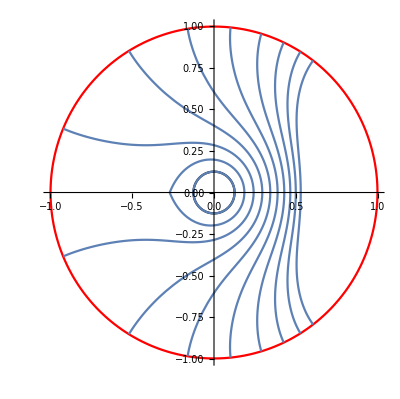
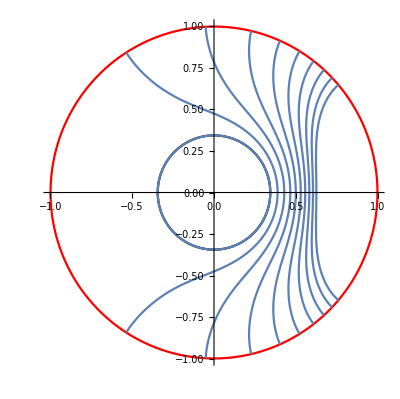
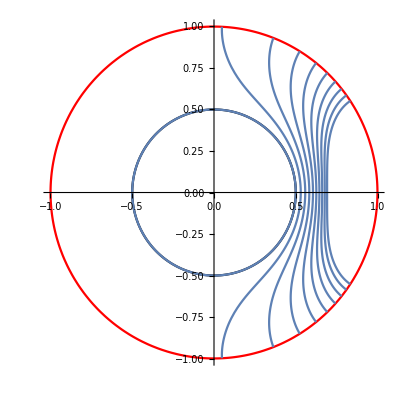
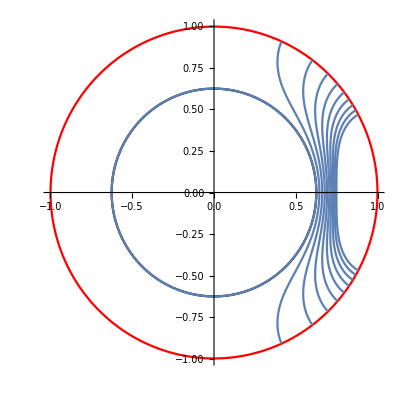

```mathematica
Table[Show[Horizonboundaryads[h⟦k⟧],Sequence@@(Evaluate[Table[Geodesic[h⟦k⟧,l],{l,h⟦k⟧+10^-10,h⟦k⟧+1,10^-1}]])],{k,Length@h}]
```

In more detail for “rh=1”

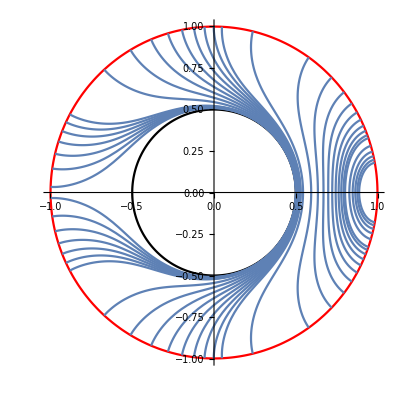

```mathematica
Show[Horizonboundaryads[h⟦3⟧],Sequence@@(Evaluate[Table[Geodesic[h⟦3⟧,l],{l,1.004,1.010,0.001}]]),Sequence@@(Evaluate[Table[Geodesic[h⟦3⟧,l],{l,1.02,1.1,0.01}]]),Sequence@@(Evaluate[Table[Geodesic[h⟦3⟧,l],{l,1.15,3,0.2}]]),Sequence@@(Evaluate[Table[Geodesic[h⟦3⟧,l],{l,3.1,6,0.5}]])]
```

Computing EE=length of geodesic numerically

```mathematica
Clear[S]
S[Rh_,ro_]:=S[Rh,ro]=NIntegrate[(Lagran/.rh->Rh)/.d->2/.{r->(Geor[Rh,ro][#]&)},{θ,0,Θo[Rh,ro]}]
```

Comparing numerical and analytical result for EE (approx 1 min)

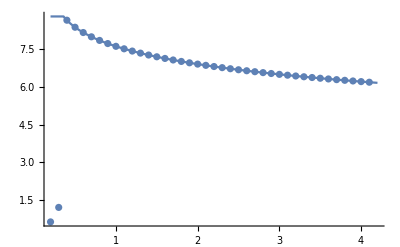
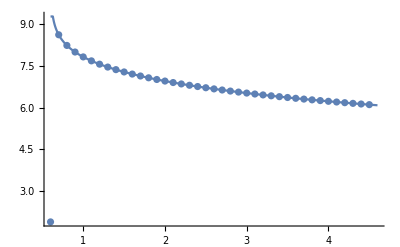
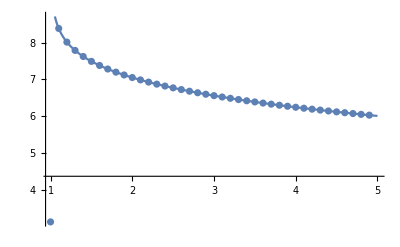
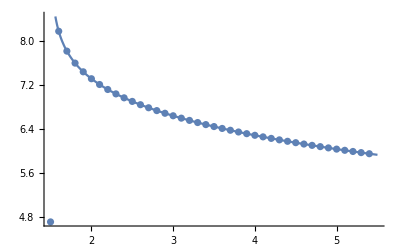

```mathematica
Table[Show[ListPlot@Table[{ro,S[h⟦k⟧,ro]},{ro,h⟦k⟧+10^-10,h⟦k⟧+4,10^-1}],Plot[Log[(2Rmax)/h⟦k⟧ Sinh[h⟦k⟧Θo[h⟦k⟧,ro]]],{ro,h⟦k⟧+10^-10,h⟦k⟧+4}],PlotRange->All] ,{k,Length@h}]
```

Function Ro: minimal radius as a function of interval opening angle θo

```mathematica
Clear[Ro]
(Ro=Table[(DeleteDuplicatesBy[Table[{Θo[h⟦k⟧,ro],ro},{ro,h⟦k⟧+10^-10,h⟦k⟧+20,10^-2}],First]//Interpolation[#]&),{k,Length@h}])
```

{InterpolatingFunction[{{0.049521, 3.14159}}, <>],InterpolatingFunction[{{0.0485707, 3.14159}}, <>],InterpolatingFunction[{{0.0476673, 3.14159}}, <>],InterpolatingFunction[{{0.0465983, 3.14159}}, <>]}

```mathematica
Araki-Lieb  Inequality  ;
```

Plotting Abs[S(θo)-S(π-θo)]-S_BH to find the transition of saddle point (approx 2 min)

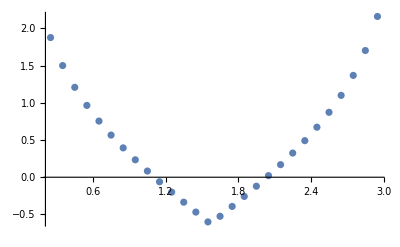
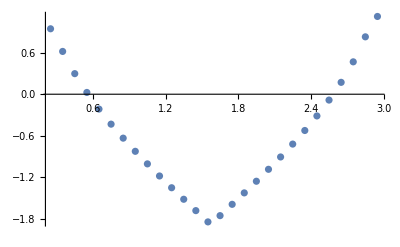
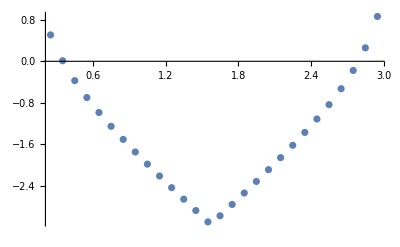
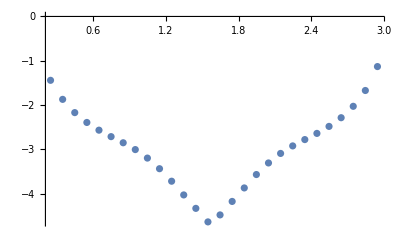

```mathematica
(Araliebplots=Table[ListPlot[Table[{θ1,Abs[S[h⟦k⟧,Ro⟦k⟧[θ1]]-S[h⟦k⟧,Ro⟦k⟧[π-θ1]]]-π h⟦k⟧},{θ1,Max[Ro⟦k⟧⟦1,1,1⟧,π-Ro⟦k⟧⟦1,1,2⟧]+2/10,Min[Ro⟦k⟧⟦1,1,2⟧,π-Ro⟦k⟧⟦1,1,1⟧]-1/10,1/10}],PlotRange->All],{k,Length@h}])
```

Points above the horizontal axis violate the bound

Numerically finding θo for which the inequality saturates (choosing starting points from the Araliebplots)

```mathematica
startθ={2.0,2.5,2.7,3.0};
```

```mathematica
Table[FindRoot[Evaluate[S[h⟦k⟧,Ro⟦k⟧[θo]]-S[h⟦k⟧,Ro⟦k⟧[π-θo]]==π h⟦k⟧],{θo,startθ⟦k⟧}]//Quiet//Timing,{k,Length@startθ}]
```

{{15.0697,{θo→2.03486}},{13.5565,{θo→2.58296}},{15.9121,{θo→2.79135}},{13.5721,{θo→3.05509}}}

Comparing with analitycal result

```mathematica
Transitionθ=Table[θo->1/h⟦k⟧ArcCoth[2Coth[π h⟦k⟧]-1],{k,Length@h}]
```

{θo→2.03486,θo→2.58296,θo→2.79595,θo→2.91057}

“GeodesicC” plots the surface or geodesic of the complement interval

```mathematica
Clear[GeodesicC]
GeodesicC[rh_,ro_]:=GeodesicC[rh,ro]=Show[PolarPlot[2/π ArcTan[Geor[rh,ro][π-x]],{x,π-Θo[rh,ro],π-Geor[rh,ro]⟦1,1,1⟧},PlotStyle->Green],PolarPlot[2/π ArcTan[Geor[rh,ro][x-π]],{x,π+Geor[rh,ro]⟦1,1,1⟧,π+Θo[rh,ro]},PlotStyle->Green]]
```

Plotting simulation of transition for horizon r_h=1

```mathematica
Manipulate[Show[Horizonboundaryads[h⟦3⟧],GeodesicC[h⟦3⟧,Ro⟦3⟧[π-(Geor[h⟦3⟧,Ro⟦3⟧[θo]]⟦1,1,2⟧)]],Geodesic[h⟦3⟧,Ro⟦3⟧[θo]]],{θo,.45,3.1,0.1}]
```

## RT in AdS_4 black hole

```mathematica
Clear[ro,rh,eulereq3,eq3,Θo3,Geor3,Geodesic3,h3]
```

extremizing the area for d=3:

```mathematica
eq3[rh_]=(r''[θ]-(eulereq/.d->3/.{r''[θ]->y}//Solve[#==0,y]&//FullSimplify)⟦1,1,2⟧)
```

-((4 r[θ] (-rh (1+rh^2)+r[θ]+r[θ]^3)^2+2 Cot[θ] r[θ] (rh+rh^3-r[θ] (1+r[θ]^2)) r'[θ]+(-5 (rh+rh^3)+6 r[θ]+8 r[θ]^3) r'[θ]^2-2 Cot[θ] r'[θ]^3)/(2 r[θ] (-rh (1+rh^2)+r[θ]+r[θ]^3)))+r''[θ]

RT surface  “ Geor3” and opening angle: “Θo3[ro]”

```mathematica
Clear[Geor3,Θo3,zero]
zero=10^-16;
Geor3[rh_,ro_]:=Geor3[rh,ro]=NDSolve[{eq3[rh]==0,r[zero]==ro,r'[zero]==0,WhenEvent[r[θ]==Rmax,θ;"StopIntegration"]},r,{θ,zero,π-zero},AccuracyGoal->16]⟦1,1,2⟧//Quiet
Θo3[rh_,ro_]:=Θo3[rh,ro]=Geor3[rh,ro]⟦1,1,2⟧
```

Computing and Memorizing for horizons “h”

```mathematica
Clear[h3]
h3={0.5,1.0,3.0,5.0};
```

```mathematica
(Table[Geor3[h3⟦Hr⟧,ro],{Hr,Length@h},{k,2,15,1},{ro,h3⟦Hr⟧+10^-k,h3⟦Hr⟧+10^(-k+1),10^-k}]//Timing)⟦1⟧
```

12.6361

Function Geodesic3 makes a plot

```mathematica
Clear[Geodesic3]
Geodesic3[rh_,ro_]:=Geodesic3[rh,ro]=Show[PolarPlot[2/π ArcTan[Geor3[rh,ro][x]],{x,Geor3[rh,ro]⟦1,1,1⟧,Θo3[rh,ro]}],PolarPlot[2/π ArcTan[Geor3[rh,ro][2π-x]],{x,2π-Θo3[rh,ro],2π-Geor3[rh,ro]⟦1,1,1⟧}]]
```

Plotting RT surfaces for a fix ϕ angle (ϕ corresponds to the extra dimension)

```mathematica
h3
```

{0.5,1.,3.,5.}

For higher dimensions the connected RT surface stops existing at a maximum opening angle θ_m.
For a fix dimension(d=3) the angle  θ_m increases with the position of the horizon r_h  (see reference [6] of problem sheet)

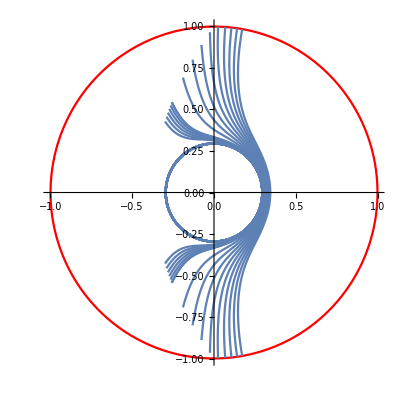
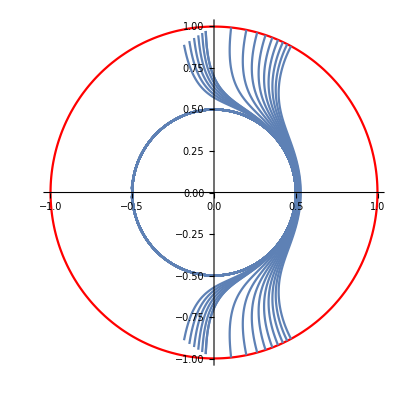
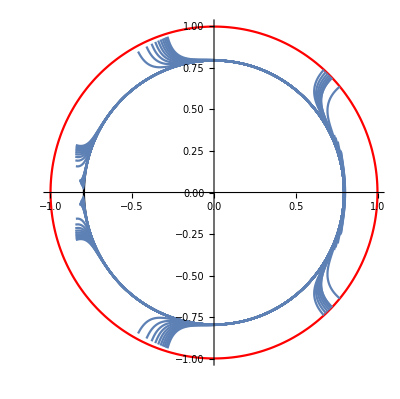
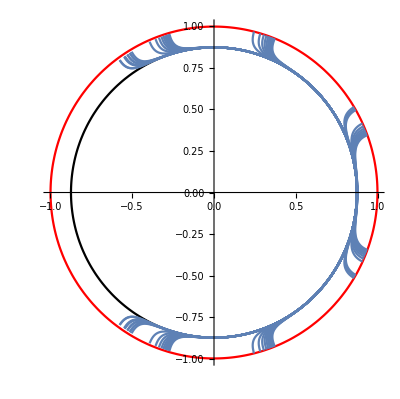

```mathematica
Table[Show[Horizonboundaryads[h3⟦Ho⟧],Sequence@@(Evaluate[Table[Geodesic3[h3⟦Ho⟧,l],{l,h3⟦Ho⟧+10^-15,h3⟦Ho⟧+10^-14,10^-15}]]),Sequence@@(Evaluate[Table[Geodesic3[h3⟦Ho⟧,l],{l,h3⟦Ho⟧+10^-13,h3⟦Ho⟧+10^-12,10^-13}]]),Sequence@@(Evaluate[Table[Geodesic3[h3⟦Ho⟧,l],{l,h3⟦Ho⟧+10^-8,h3⟦Ho⟧+10^-7,10^-8}]]),Sequence@@(Evaluate[Table[Geodesic3[h3⟦Ho⟧,l],{l,h3⟦Ho⟧+10^-2,h3⟦Ho⟧+10^-1,10^-2}]]),
Sequence@@(Evaluate[Table[Geodesic3[h3⟦Ho⟧,l],{l,h3⟦Ho⟧+5 10^-3,h3⟦Ho⟧+10^-2,10^-3}]]),PlotRange->All],{Ho,Length@h}]
```